# Analisi della risposta libera, caso TD, autovalori multipli

```mathematica
ClearAll["Global`*"]
```

```mathematica
A={{-16/45,38/45,7/45,7/45},{8/45,-1/45,-8/45,-8/45},{1,-1,-1/5,0},{-68/45,67/45,23/45,14/45}}
```

{{-16/45,38/45,7/45,7/45},{8/45,-1/45,-8/45,-8/45},{1,-1,-1/5,0},{-68/45,67/45,23/45,14/45}}

```mathematica
A//MatrixForm
```

(-16/45 | 38/45 | 7/45 | 7/45
8/45 | -1/45 | -8/45 | -8/45
1 | -1 | -1/5 | 0
-68/45 | 67/45 | 23/45 | 14/45)

Mi calcolo lo spettro di A

```mathematica
Eigenvalues[A]
```

{1/3,-1/5,-1/5,-1/5}

```mathematica
MatrixMinimalPolynomial[a_List?MatrixQ,x_]:=Module[{i,n=1,qu={},mnm={Flatten[IdentityMatrix[Length[a]]]}},While[Length[qu]==0,AppendTo[mnm,Flatten[MatrixPower[a,n]]];
qu=NullSpace[Transpose[mnm]];
n++];
First[qu].Table[x^i,{i,0,n-1}]]
```

```mathematica
Factor[MatrixMinimalPolynomial[A,x]]
```

1/375 (-1+3 x) (1+5 x)^3

```mathematica
Factor[CharacteristicPolynomial[A,x]]
```

1/375 (-1+3 x) (1+5 x)^3

Mi calcolo intanto la forma di Jordan di A

```mathematica
{T,Λ}=JordanDecomposition[A]
```

{{{0,-1,-2,-1},{0,0,-1,-1},{-1,-1,-3,0},{1,0,0,1}},{{-1/5,1,0,0},{0,-1/5,1,0},{0,0,-1/5,0},{0,0,0,1/3}}}

```mathematica
Λ//MatrixForm
```

(-1/5 | 1 | 0 | 0
0 | -1/5 | 1 | 0
0 | 0 | -1/5 | 0
0 | 0 | 0 | 1/3)

```mathematica
T//MatrixForm
```

(0 | -1 | -2 | -1
0 | 0 | -1 | -1
-1 | -1 | -3 | 0
1 | 0 | 0 | 1)

```mathematica
MatrixPower[Λ,k]//MatrixForm
```

((-1/5)^k | -(-1)^k 5^(1-k) k | 1/2 (-1)^k 5^(2-k) (-1+k) k | 0
0 | (-1/5)^k | -(-1)^k 5^(1-k) k | 0
0 | 0 | (-1/5)^k | 0
0 | 0 | 0 | 3^-k)

```mathematica
Subscript[x, 0]={{1},{0},{0},{1}}
```

{{1},{0},{0},{1}}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{1},{-1},{0},{0}}

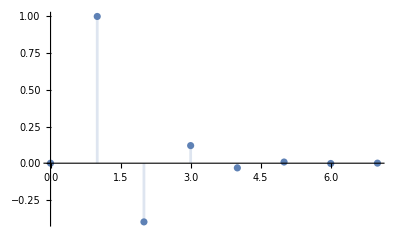

```mathematica
DiscretePlot[Binomial[k,1](-1/5)^(k-1),{k,0,7},PlotRange->All]
```

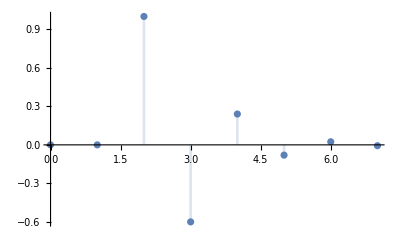

```mathematica
DiscretePlot[Binomial[k,2](-1/5)^(k-2),{k,0,7},PlotRange->All]
```

Calcolo la risposta libera

```mathematica
C1={1,0,1,0}
```

{1,0,1,0}

```mathematica
Subscript[x, l][k_]:=Simplify[T.MatrixPower[Λ,k].Subscript[z, 0]]
```

```mathematica
Subscript[y, l][k_]:=Simplify[C1.Subscript[x, l][k]]
```

```mathematica
Subscript[x, l][k]//MatrixForm
```

((-1/5)^k
0
-(-1)^k 5^(1-k) k
(-1/5)^k (1+5 k))

```mathematica
Subscript[z, 0]
```

{{1},{-1},{0},{0}}